1.3

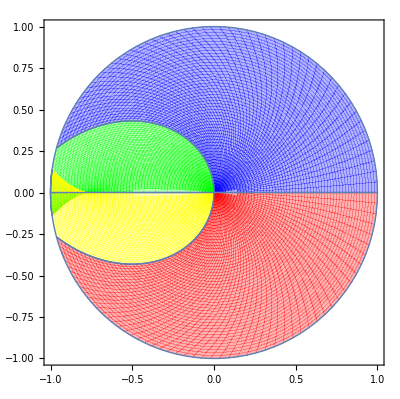

```mathematica
colors = {Blue,Green,Yellow,Red};
n = Length[colors];
ν = 1.3

disk = Table[ParametricPlot[{r Cos[θ+ν r Sin[θ]],r Sin[θ+ν r Sin[θ]]},{r,0,1},{θ,i 2 π/n,(i+1)2π/n},PlotStyle->colors[[i+1]]],{i,0,n-1}];
Show[disk,PlotRange-> All]
```

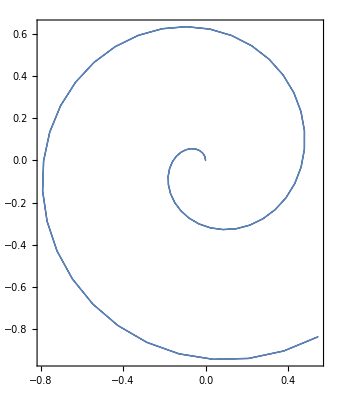
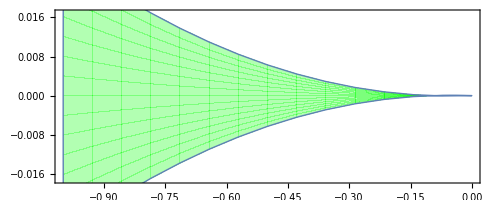
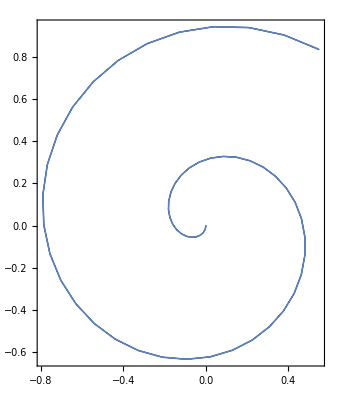
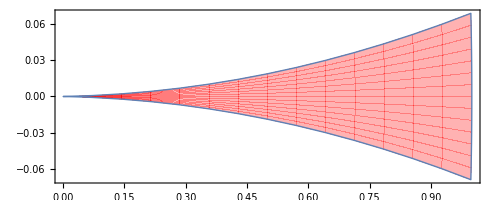

```mathematica
prop  = Table[ParametricPlot[{r Cos[θ+ν r Sin[θ]],r Sin[θ+ν r Sin[θ]]},{r,0,1},{θ,0.999i 2  π/n,1.001 2i π/n},PlotStyle->colors[[i]]],{i,1,n}]
```

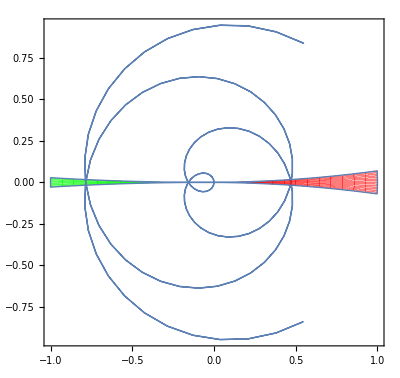

```mathematica
Show[prop,PlotRange-> All]
```

```mathematica
anlist = Table[disk =Table[ParametricPlot[{r Cos[θ+ν r Sin[θ]],r Sin[θ+ν r Sin[θ]]},{r,0,1},{θ,i 2 π/n,(i+1)2π/n},PlotStyle->colors[[i+1]]],{i,0,n-1}];
Show[disk,PlotRange-> All],{ν,0.1,10,0.1}]
```